```mathematica
Вариант 7  Шего
№1
```

```mathematica
N[ⅇ^2]
```

7.38906

```mathematica
N[π^2]
```

9.8696

```mathematica
N[Log[2,7]]
```

2.80735

```mathematica
2^30
```

1073741824

```mathematica
№2
```

```mathematica
FactorInteger[123456789123456789]
```

{{3,2},{7,1},{11,1},{13,1},{19,1},{3607,1},{3803,1},{52579,1}}

```mathematica
FactorInteger[25739445264]
```

{{2,4},{3,1},{13,1},{41249111,1}}

```mathematica
Factor[x^4+y^4+z^4-2x^2y^2-2x^2z^2-2y^2z^2]
```

(x-y-z) (x+y-z) (x-y+z) (x+y+z)

```mathematica
Factor[(x+y+z)^3-x^3-y^3-z^3]
```

3 (x+y) (x+z) (y+z)

```mathematica
№3
```

```mathematica
Simplify[1/(1-x)+1/(1+x)+2/(1+x^2)+4/(1+x^4)+8/(1+x^8)+16/(1+x^16)]
```

-32/(-1+x^32)

```mathematica
Simplify[1/(x(x+1))+1/((x+2)(x+1))+1/((x+2)(x+3))+1/((x+3)(x+4))+1/((x+5)(x+4))]
```

```mathematica
5/(5 x+x^2)
```

```mathematica
№4
```

```mathematica
Вместо a подставлено натуральное число 5
```

```mathematica
Solve[5x^10+x^2==0]
```

{{x→0},{x→0},{x→-(-1/5)^(1/8)},{x→(-1/5)^(1/8)},{x→-(-1)^(3/8)/5^(1/8)},{x→(-1)^(3/8)/5^(1/8)},{x→-(-1)^(5/8)/5^(1/8)},{x→(-1)^(5/8)/5^(1/8)},{x→-(-1)^(7/8)/5^(1/8)},{x→(-1)^(7/8)/5^(1/8)}}

```mathematica
Clear[a]
```

```mathematica
Solve[x^3-3x+2==0]
```

{{x→-2},{x→1},{x→1}}

```mathematica
№5
```

```mathematica
Вместо n у меня будет 3, то есть будем находить проихводную третьего порядка
```

```mathematica
D[Sin[x], {x,3}]
```

-Cos[x]

```mathematica
D[Cos[2x],{x,3}]
```

8 Sin[2 x]

```mathematica
D[1/(1+x),{x,3}]
```

-6/(1+x)^4

```mathematica
D[ⅇ^(-3x),{x,3}]
```

-27 ⅇ^(-3 x)

```mathematica
№6
```

```mathematica
∫√(3-2x-x^2)ⅆx
```

1/2 (1+x) √(3-2 x-x^2)-4 ArcTan[(√(3-2 x-x^2))/(3+x)]

```mathematica
∫_-1^1 x^2/(x+2)ⅆx
```

```mathematica
-4+Log[81]
```

```mathematica
Clear[y]
```

```mathematica
∫_(x^2+y^2<=1)^5 ∫Log10[10]ⅆxⅆy
```

x (5-(x^2+y^2≤1))

```mathematica
№7
```

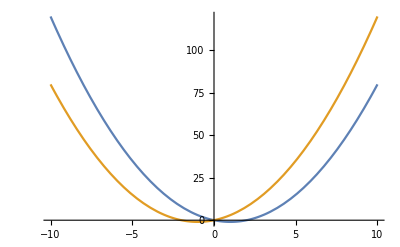

```mathematica
Plot[{{t^2-2t},{t^2+2t}},{t,-10,10}]
```

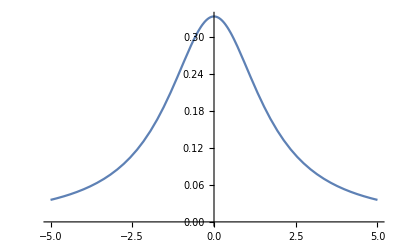

```mathematica
Plot[1/(x^2+3),{x,-5,5}]
```

```mathematica
Аналогично, но только через y, то есть я присвоил переменной функцию
```

```mathematica
y =1/(x^2+3)
```

1/(3+x^2)

```mathematica
Plot[y,{x,-5,5}]
```

-Graphics-

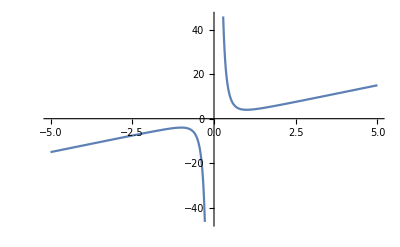

```mathematica
Plot[(3x^4+1)/x^3,{x,-5,5}]
```

```mathematica
№8
```

```mathematica
y = {{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
y // MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
Eigenvectors[y]
```

```mathematica
{{-(-15-√33)/(33+7 √33),(4 (6+√33))/(33+7 √33),1},{-(15-√33)/(-33+7 √33),(4 (-6+√33))/(-33+7 √33),1},{1,-2,1}}
```

```mathematica
Eigenvalues[y]
```

{3/2 (5+√33),3/2 (5-√33),0}

```mathematica
b = {1,1,1}
```

{1,1,1}

```mathematica
LinearSolve[y,b]
```

{-1,1,0}

```mathematica
№9
```

```mathematica
K= {1,0,7,9,6,3,2}
```

{1,0,7,9,6,3,2}

```mathematica
Delete[K,{{6},{7}}]
```

{1,0,7,9,6}

```mathematica
№10
```

```mathematica
FindMaximum[{x+2y,x^2+y^2==5},{x,y}]
```

{5.,{x→1.,x→2.}}

```mathematica
FindMinimum[{x+2y,x^2+y^2==5},{x,y}]
```

{-5.,{x→-1.,x→-2.}}

```mathematica
Maximize[{x+2y,x^2+y^2==5},{x,y}]
```

{3 √(5/2),{x→√(5/2)}}

```mathematica
Minimize[{x+2y,x^2+y^2==5},{x,y}]
```

{-3 √(5/2),{x→-√(5/2)}}